# Computer Lab 5: Lecture 14

In our computer lab lectures we will work together through concepts and challanges we have discussed over the week in class.  As with your after-class Exercises, you will be expected to turn in your computer lab notebooks before the nect lecture. Please do so by e-mailing your completed *nb file to Lan Yu (ece329.uiuc@gmail.com), make sure you name the file using the following notation: “Exn_Last_First.nb”, where n is the Lecture number (in this case, 14), and First and Last would be your first and last name.  So my submission to Lan for this computer lab would be titled “Ex14_Wasserman_Dan.nb”.  You will receive full credit for your computer lab if it is turned in before the next lecture (Lecture n+1).  For this Computer Lab you will need to submit BOTH your “Ex14_Wasserman_Dan.nb” and your “Wasserman_Dan_CDF.cdf” files.  No late submissions will be accepted.

## Objective/Overview:

In class this week we were introduced to magnetic fields.  We learned that magnetic fields are caused by currents, and can exert a force on moving charges.  We determined that we can calculate the magnetic field from an infinite wire (straight line), as well as from an current carrying wire of arbitrary shape, using the Biot Savart Law.  We also showed that Ampere’s Law allows us to calculate magnetic fields for current distributions with certain symmetries, in a very similar way to how we can use Gauss’s Law to calculate electric or displacement fields.  In our last exercise, you also got to see how changes in magnetic field can induce electromotive forces (emf) on wire loops.  In today’s exercise, we are going to go back to looking at loops, but this time we are going to assume we have a current flowing in the loop(s), and then calculate the resulting magnetic field.

## Calculating the Magnetic Field from a single Current Loop (Using BS Law)

We know we can calculate the magnetic field from any current carrying wire using the Biot-Savart Law:
dB⃗=(μ_o I)/(4π)(ⅆ l⃗×r⃗)/r^3=(μ_o I)/(4π)(ⅆ l⃗×r̂)/r^2
We need to find the magnetic field from a loop of current, so let’s say that our loop is on the xy plane, with the z-axis going through the center of the loop and a loop radius of ro.  We are basically going to have to take a line integral around the loop.  Our loop is defined by:

```mathematica
ClearAll[ropath,ro,dropath,po,bloop,r]
```

```mathematica
ropath[ro_]:={ro*Cos[2*Pi*t],ro*Sin[2*Pi*t],0}
```

```mathematica
ropath[ro]
```

{ro Cos[2 π t],ro Sin[2 π t],0}

our ⅆ l⃗is then just:

```mathematica
dropath[ro_]:=D[ropath[ro],t]
```

```mathematica
dropath[ro]
```

{-2 π ro Sin[2 π t],2 π ro Cos[2 π t],0}

Now we need to integrate around this loop, with r⃗={x_o,y_o,z_o)=-{ro Cos[2 π t],ro Sin[2 π t],0},  ⅆ l⃗=dropath, and let’s set (μ_o I)/(4π)=1 and ro=1.  Let’s stay in the xz plane to simplify things...

```mathematica
po={xo,0,zo}
```

{xo,0,zo}

```mathematica
r=po-ropath[1]
```

{xo-Cos[2 π t],-Sin[2 π t],zo}

```mathematica
rhat=Normalize[r]
```

{(xo-Cos[2 π t])/(√(Abs[zo]^2+Abs[xo-Cos[2 π t]]^2+Abs[Sin[2 π t]]^2)),-Sin[2 π t]/(√(Abs[zo]^2+Abs[xo-Cos[2 π t]]^2+Abs[Sin[2 π t]]^2)),zo/(√(Abs[zo]^2+Abs[xo-Cos[2 π t]]^2+Abs[Sin[2 π t]]^2))}

```mathematica
rhat={(xo-Cos[2 π t])/(√((zo)^2+(xo-Cos[2 π t])^2+(Sin[2 π t])^2)),-Sin[2 π t]/(√((zo)^2+(xo-Cos[2 π t])^2+(Sin[2 π t])^2)),zo/(√((zo)^2+(xo-Cos[2 π t])^2+(Sin[2 π t])^2))}
```

{(xo-Cos[2 π t])/(√(zo^2+(xo-Cos[2 π t])^2+Sin[2 π t]^2)),-Sin[2 π t]/(√(zo^2+(xo-Cos[2 π t])^2+Sin[2 π t]^2)),zo/(√(zo^2+(xo-Cos[2 π t])^2+Sin[2 π t]^2))}

We now have everything we need to solve the integral which will give us B(xo,zo).  Unfortunately, this will hang Mathematica.  It doesn’t like the integral.  But we can solve for certain values of xo, zo using the following syntax:

```mathematica
bloop[x_,z_]:=NIntegrate[Cross[dropath[1],rhat]/Dot[r,r]/.{xo->x,zo->z},{t,0,1},AccuracyGoal->8]
```

Can we plot this along some lines, say the z-axis?

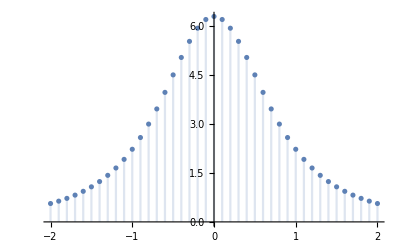

```mathematica
DiscretePlot[bloop[0,z][[3]],{z,-2,2,.1}]
```

The plot above shows the z-component of B as a function of position along the z-axis.  This is actually an integral that can be done analytically.
What about B_z along the x-axis?

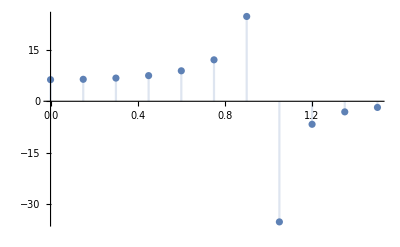

```mathematica
DiscretePlot[bloop[x,0][[3]],{x,0,1.5,.15}]
```

Note that I have tried to avoid xo=+/-1, where B diverges...Nonetheless, this still took a pretty long time.  We see that across the x axis, our B field is pretty much constant inside the loop (ignoring the divergence at xo=+/-1), and ~0 outside!!  Also, bear in mind that if we want to find the field at any point in 3D space, we can recognize that this is a symmetric structure, so all that matters will be the distance from the z axis and the distance above the xy plane.
Trying to take the integral symbolically is a total mess!  It requires Elliptical Integrals and Mathematica slows to a crawl.
Even with the faster NIntegrate command, it will still be incredibly difficult to produce even a VectorPlot for this system.  We can try to do so, as long as we don’t use too many points...

```mathematica
v1=Table[{{x,z},bloop[x,z][[{1,3}]]},{x,0,1.5,.15},{z,-.5,1.5,.25}]
```

{{{{0.,-0.5},{-1.05452×10^-17,4.49588}},{{0.,-0.25},{-1.11123×10^-16,5.73702}},{{0.,0.},{0.,6.28319}},{{0.,0.25},{1.11123×10^-16,5.73702}},{{0.,0.5},{1.05452×10^-17,4.49588}},{{0.,0.75},{2.08679×10^-16,3.21699}},{{0.,1.},{1.5808×10^-16,2.22144}},{{0.,1.25},{8.63817×10^-17,1.53174}},{{0.,1.5},{6.14215×10^-17,1.0724}}},{{{0.15,-0.5},{-0.411934,4.49488}},{{0.15,-0.25},{-0.314383,5.80178}},{{0.15,0.},{0.,6.3915}},{{0.15,0.25},{0.314383,5.80178}},{{0.15,0.5},{0.411934,4.49488}},{{0.15,0.75},{0.348875,3.18858}},{{0.15,1.},{0.249003,2.19318}},{{0.15,1.25},{0.16694,1.51109}},{{0.15,1.5},{0.110475,1.05874}}},{{{0.3,-0.5},{-0.867997,4.47883}},{{0.3,-0.25},{-0.699293,6.00072}},{{0.3,0.},{0.,6.74652}},{{0.3,0.25},{0.699293,6.00072}},{{0.3,0.5},{0.867997,4.47883}},{{0.3,0.75},{0.704862,3.096}},{{0.3,1.},{0.491845,2.10682}},{{0.3,1.25},{0.326657,1.44952}},{{0.3,1.5},{0.215621,1.01838}}},{{{0.45,-0.5},{-1.41106,4.40102}},{{0.45,-0.25},{-1.26405,6.34045}},{{0.45,0.},{0.,7.46316}},{{0.45,0.25},{1.26405,6.34045}},{{0.45,0.5},{1.41106,4.40102}},{{0.45,0.75},{1.06673,2.91814}},{{0.45,1.},{0.718999,1.95889}},{{0.45,1.25},{0.47126,1.34849}},{{0.45,1.5},{0.310193,0.953259}}},{{{0.6,-0.5},{-2.06436,4.15981}},{{0.6,-0.25},{-2.22633,6.78055}},{{0.6,0.},{0.,8.86302}},{{0.6,0.25},{2.22633,6.78055}},{{0.6,0.5},{2.06436,4.15981}},{{0.6,0.75},{1.41428,2.62572}},{{0.6,1.},{0.915336,1.74781}},{{0.6,1.25},{0.592109,1.21181}},{{0.6,1.5},{0.389282,0.866825}}},{{{0.75,-0.5},{-2.76558,3.58852}},{{0.75,-0.25},{-4.01275,6.97786}},{{0.75,0.},{0.,12.0546}},{{0.75,0.25},{4.01275,6.97786}},{{0.75,0.5},{2.76558,3.58852}},{{0.75,0.75},{1.69892,2.19864}},{{0.75,1.},{1.0609,1.47985}},{{0.75,1.25},{0.680786,1.04685}},{{0.75,1.5},{0.448825,0.764178}}},{{{0.9,-0.5},{-3.26072,2.56219}},{{0.9,-0.25},{-6.72497,5.39445}},{{0.9,0.},{0.,24.6673}},{{0.9,0.25},{6.72497,5.39445}},{{0.9,0.5},{3.26072,2.56219}},{{0.9,0.75},{1.85113,1.65714}},{{0.9,1.},{1.13662,1.17423}},{{0.9,1.25},{0.731111,0.865021}},{{0.9,1.5},{0.486288,0.651844}}},{{{1.05,-0.5},{-3.20109,1.28749}},{{1.05,-0.25},{-7.05099,0.863244}},{{1.05,0.},{0.,-35.0787}},{{1.05,0.25},{7.05099,0.863244}},{{1.05,0.5},{3.20109,1.28749}},{{1.05,0.75},{1.82121,1.08153}},{{1.05,1.},{1.1338,0.862406}},{{1.05,1.25},{0.74142,0.680596}},{{1.05,1.5},{0.501259,0.537093}}},{{{1.2,-0.5},{-2.60522,0.271688}},{{1.2,-0.25},{-4.10362,-1.54958}},{{1.2,0.},{0.,-6.69063}},{{1.2,0.25},{4.10362,-1.54958}},{{1.2,0.5},{2.60522,0.271688}},{{1.2,0.75},{1.62679,0.579261}},{{1.2,1.},{1.06088,0.578648}},{{1.2,1.25},{0.715717,0.507773}},{{1.2,1.5},{0.495634,0.4269}}},{{{1.35,-0.5},{-1.87271,-0.255406}},{{1.35,-0.25},{-2.06282,-1.59387}},{{1.35,0.},{0.,-3.08093}},{{1.35,0.25},{2.06282,-1.59387}},{{1.35,0.5},{1.87271,-0.255406}},{{1.35,0.75},{1.34539,0.217524}},{{1.35,1.},{0.940843,0.347383}},{{1.35,1.25},{0.662735,0.357427}},{{1.35,1.5},{0.473225,0.326876}}},{{{1.5,-0.5},{-1.27988,-0.434272}},{{1.5,-0.25},{-1.1042,-1.22496}},{{1.5,0.},{0.,-1.78912}},{{1.5,0.25},{1.1042,-1.22496}},{{1.5,0.5},{1.27988,-0.434272}},{{1.5,0.75},{1.0577,-0.00255854}},{{1.5,1.},{0.800878,0.176679}},{{1.5,1.25},{0.593317,0.235165}},{{1.5,1.5},{0.438912,0.240583}}}}

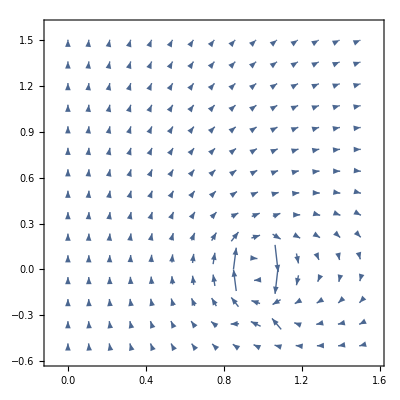

```mathematica
ListVectorPlot[v1]
```

This wasn’t easy, but we were able to plot the magnetic field from a single loop.  You will notice that the vector plot has a MUCH higher density than our table.  Clearly Mathematica has interpolated the table to create a denser array of data points.  Below are plotted only the points in the table:

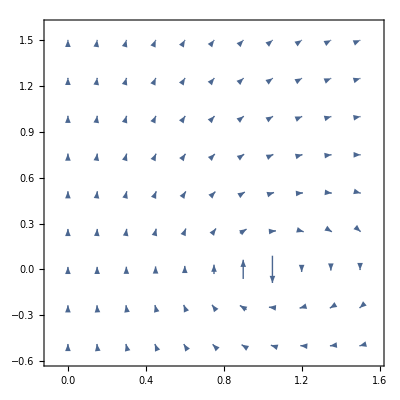

```mathematica
ListVectorPlot[v1,VectorPoints->All]
```

## Calculating the Magnetic Field from More than One Current Loop (Using BS Law)

What about more than one loop? Well, we know that magnetic fields can be superpositioned, so all we need to do is add the field from our single loop to the field from another loop, but shifted...Of course, if we perform the integrals above for each point, for each loop, we are adding a lot of time to the calculation.  On the other hand, if we take the table, and shift the table, we are losing a lot of resolution...
Let’s start by simply adding a second loop, at z=.5.

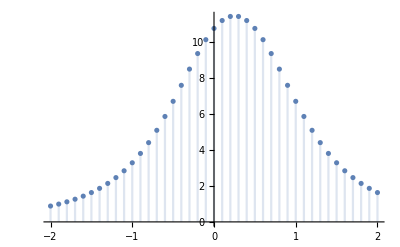

```mathematica
DiscretePlot[bloop[0,z][[3]]+bloop[0,z-0.5][[3]],{z,-2,2,.1}]
```

Can we do a vector plot of this?  Well, it’s going to get slow, quickly, but we can try...

```mathematica
v2=Table[{{x,z},bloop[x,z][[{1,3}]]+bloop[x,z-0.5][[{1,3}]]},{x,0,1.5,.15},{z,-.5,1.5,.25}]
```

{{{{0.,-0.5},{-1.68626×10^-16,6.71732}},{{0.,-0.25},{-3.19802×10^-16,8.95401}},{{0.,0.},{-1.05452×10^-17,10.7791}},{{0.,0.25},{0.,11.474}},{{0.,0.5},{1.05452×10^-17,10.7791}},{{0.,0.75},{3.19802×10^-16,8.95401}},{{0.,1.},{1.68626×10^-16,6.71732}},{{0.,1.25},{2.95061×10^-16,4.74873}},{{0.,1.5},{2.19502×10^-16,3.29384}}},{{{0.15,-0.5},{-0.660937,6.68806}},{{0.15,-0.25},{-0.663258,8.99036}},{{0.15,0.},{-0.411934,10.8864}},{{0.15,0.25},{0.,11.6036}},{{0.15,0.5},{0.411934,10.8864}},{{0.15,0.75},{0.663258,8.99036}},{{0.15,1.},{0.660937,6.68806}},{{0.15,1.25},{0.515815,4.69967}},{{0.15,1.5},{0.359478,3.25192}}},{{{0.3,-0.5},{-1.35984,6.58565}},{{0.3,-0.25},{-1.40416,9.09671}},{{0.3,0.},{-0.867997,11.2254}},{{0.3,0.25},{0.,12.0014}},{{0.3,0.5},{0.867997,11.2254}},{{0.3,0.75},{1.40416,9.09671}},{{0.3,1.},{1.35984,6.58565}},{{0.3,1.25},{1.03152,4.54551}},{{0.3,1.5},{0.707466,3.12521}}},{{{0.45,-0.5},{-2.13006,6.35991}},{{0.45,-0.25},{-2.33078,9.25859}},{{0.45,0.},{-1.41106,11.8642}},{{0.45,0.25},{0.,12.6809}},{{0.45,0.5},{1.41106,11.8642}},{{0.45,0.75},{2.33078,9.25859}},{{0.45,1.},{2.13006,6.35991}},{{0.45,1.25},{1.53799,4.26663}},{{0.45,1.5},{1.02919,2.91214}}},{{{0.6,-0.5},{-2.9797,5.90762}},{{0.6,-0.25},{-3.64061,9.40626}},{{0.6,0.},{-2.06436,13.0228}},{{0.6,0.25},{0.,13.5611}},{{0.6,0.5},{2.06436,13.0228}},{{0.6,0.75},{3.64061,9.40626}},{{0.6,1.},{2.9797,5.90762}},{{0.6,1.25},{2.00638,3.83753}},{{0.6,1.5},{1.30462,2.61463}}},{{{0.75,-0.5},{-3.82648,5.06837}},{{0.75,-0.25},{-5.71167,9.17651}},{{0.75,0.},{-2.76558,15.6431}},{{0.75,0.25},{0.,13.9557}},{{0.75,0.5},{2.76558,15.6431}},{{0.75,0.75},{5.71167,9.17651}},{{0.75,1.},{3.82648,5.06837}},{{0.75,1.25},{2.3797,3.24549}},{{0.75,1.5},{1.50972,2.24403}}},{{{0.9,-0.5},{-4.39734,3.73642}},{{0.9,-0.25},{-8.57611,7.05158}},{{0.9,0.},{-3.26072,27.2295}},{{0.9,0.25},{0.,10.7889}},{{0.9,0.5},{3.26072,27.2295}},{{0.9,0.75},{8.57611,7.05158}},{{0.9,1.},{4.39734,3.73642}},{{0.9,1.25},{2.58224,2.52216}},{{0.9,1.5},{1.6229,1.82608}}},{{{1.05,-0.5},{-4.33489,2.14989}},{{1.05,-0.25},{-8.8722,1.94477}},{{1.05,0.},{-3.20109,-33.7912}},{{1.05,0.25},{0.,1.72649}},{{1.05,0.5},{3.20109,-33.7912}},{{1.05,0.75},{8.8722,1.94477}},{{1.05,1.},{4.33489,2.14989}},{{1.05,1.25},{2.56263,1.76213}},{{1.05,1.5},{1.63506,1.3995}}},{{{1.2,-0.5},{-3.66611,0.850336}},{{1.2,-0.25},{-5.73041,-0.970315}},{{1.2,0.},{-2.60522,-6.41894}},{{1.2,0.25},{0.,-3.09915}},{{1.2,0.5},{2.60522,-6.41894}},{{1.2,0.75},{5.73041,-0.970315}},{{1.2,1.},{3.66611,0.850336}},{{1.2,1.25},{2.34251,1.08703}},{{1.2,1.5},{1.55652,1.00555}}},{{{1.35,-0.5},{-2.81355,0.0919769}},{{1.35,-0.25},{-3.40821,-1.37634}},{{1.35,0.},{-1.87271,-3.33634}},{{1.35,0.25},{0.,-3.18773}},{{1.35,0.5},{1.87271,-3.33634}},{{1.35,0.75},{3.40821,-1.37634}},{{1.35,1.},{2.81355,0.0919769}},{{1.35,1.25},{2.00812,0.57495}},{{1.35,1.5},{1.41407,0.674259}}},{{{1.5,-0.5},{-2.08076,-0.257592}},{{1.5,-0.25},{-2.1619,-1.22752}},{{1.5,0.},{-1.27988,-2.22339}},{{1.5,0.25},{0.,-2.44992}},{{1.5,0.5},{1.27988,-2.22339}},{{1.5,0.75},{2.1619,-1.22752}},{{1.5,1.},{2.08076,-0.257592}},{{1.5,1.25},{1.65102,0.232606}},{{1.5,1.5},{1.23979,0.417262}}}}

Oof.  That is brutal.  But it works!

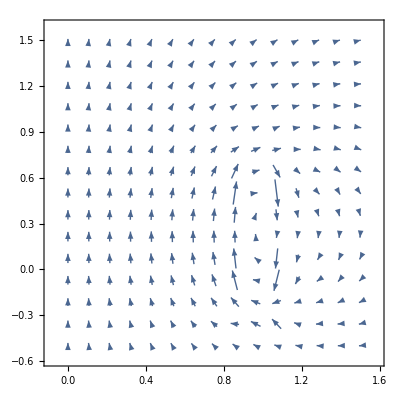

```mathematica
ListVectorPlot[v2]
```

If we want to create a solenoid, then all we have to do is add the fields from a series of shifted single loops!  But we have already seen how long it takes to do 2 loops, it is going to get unwieldy quickly. Try to see if you can model the field from a Solenoid with 6 loops equally spaced between z=0 and 1.

```mathematica
v6=Table[{{x,z},bloop[x,z][[{1,3}]]+bloop[x,z-0.2][[{1,3}]]+bloop[x,z-0.4][[{1,3}]]+bloop[x,z-0.6][[{1,3}]]+bloop[x,z-0.8][[{1,3}]]+bloop[x,z-1][[{1,3}]]},{x,0,1.5,.15},{z,-.5,1.5,.25}]
```

{{{{0.,-0.5},{-5.88533×10^-16,14.9397}},{{0.,-0.25},{-6.78486×10^-16,20.5774}},{{0.,0.},{-7.79523×10^-16,26.4112}},{{0.,0.25},{-4.20174×10^-16,30.8007}},{{0.,0.5},{-1.51682×10^-17,32.4145}},{{0.,0.75},{4.34798×10^-16,30.8007}},{{0.,1.},{7.93898×10^-16,26.4112}},{{0.,1.25},{6.13867×10^-16,20.5774}},{{0.,1.5},{5.88533×10^-16,14.9397}}},{{{0.15,-0.5},{-1.545,14.8246}},{{0.15,-0.25},{-1.81453,20.5518}},{{0.15,0.},{-1.64193,26.5452}},{{0.15,0.25},{-0.95862,31.0598}},{{0.15,0.5},{-1.11022×10^-16,32.7132}},{{0.15,0.75},{0.95862,31.0598}},{{0.15,1.},{1.64193,26.5452}},{{0.15,1.25},{1.81453,20.5518}},{{0.15,1.5},{1.545,14.8246}}},{{{0.3,-0.5},{-3.12394,14.4543}},{{0.3,-0.25},{-3.75698,20.4518}},{{0.3,0.},{-3.4336,26.9595}},{{0.3,0.25},{-1.99054,31.8624}},{{0.3,0.5},{0.,33.6292}},{{0.3,0.75},{1.99054,31.8624}},{{0.3,1.},{3.4336,26.9595}},{{0.3,1.25},{3.75698,20.4518}},{{0.3,1.5},{3.12394,14.4543}}},{{{0.45,-0.5},{-4.75303,13.7503}},{{0.45,-0.25},{-5.98044,20.1923}},{{0.45,0.},{-5.56151,27.7025}},{{0.45,0.25},{-3.16126,33.2896}},{{0.45,0.5},{-4.44089×10^-16,35.2164}},{{0.45,0.75},{3.16126,33.2896}},{{0.45,1.},{5.56151,27.7025}},{{0.45,1.25},{5.98044,20.1923}},{{0.45,1.5},{4.75303,13.7503}}},{{{0.6,-0.5},{-6.39388,12.5716}},{{0.6,-0.25},{-8.69578,19.5548}},{{0.6,0.},{-8.31208,28.9181}},{{0.6,0.25},{-4.49511,35.4938}},{{0.6,0.5},{8.88178×10^-16,37.5367}},{{0.6,0.75},{4.49511,35.4938}},{{0.6,1.},{8.31208,28.9181}},{{0.6,1.25},{8.69578,19.5548}},{{0.6,1.5},{6.39388,12.5716}}},{{{0.75,-0.5},{-7.8737,10.7384}},{{0.75,-0.25},{-12.1683,17.9288}},{{0.75,0.},{-12.2017,31.1477}},{{0.75,0.25},{-5.84281,38.6918}},{{0.75,0.5},{0.,40.5671}},{{0.75,0.75},{5.84281,38.6918}},{{0.75,1.},{12.2017,31.1477}},{{0.75,1.25},{12.1683,17.9288}},{{0.75,1.5},{7.8737,10.7384}}},{{{0.9,-0.5},{-8.79655,8.19462}},{{0.9,-0.25},{-16.0066,13.5973}},{{0.9,0.},{-17.5834,39.6464}},{{0.9,0.25},{-3.97916,42.8551}},{{0.9,0.5},{3.55271×10^-15,41.44}},{{0.9,0.75},{3.97916,42.8551}},{{0.9,1.},{17.5834,39.6464}},{{0.9,1.25},{16.0066,13.5973}},{{0.9,1.5},{8.79655,8.19462}}},{{{1.05,-0.5},{-8.71863,5.3324}},{{1.05,-0.25},{-16.2266,5.83588}},{{1.05,0.},{-18.2944,-30.3837}},{{1.05,0.25},{5.48736,-12.5071}},{{1.05,0.5},{3.55271×10^-15,-4.42112}},{{1.05,0.75},{-5.48736,-12.5071}},{{1.05,1.},{18.2944,-30.3837}},{{1.05,1.25},{16.2266,5.83588}},{{1.05,1.5},{8.71863,5.3324}}},{{{1.2,-0.5},{-7.70157,2.89465}},{{1.2,-0.25},{-11.9907,0.750561}},{{1.2,0.},{-12.1385,-7.61424}},{{1.2,0.25},{-5.46248,-10.8157}},{{1.2,0.5},{0.,-11.1964}},{{1.2,0.75},{5.46248,-10.8157}},{{1.2,1.},{12.1385,-7.61424}},{{1.2,1.25},{11.9907,0.750561}},{{1.2,1.5},{7.70157,2.89465}}},{{{1.35,-0.5},{-6.31061,1.26376}},{{1.35,-0.25},{-8.28909,-0.929807}},{{1.35,0.},{-7.80886,-5.11311}},{{1.35,0.25},{-4.14499,-7.78551}},{{1.35,0.5},{8.88178×10^-16,-8.45949}},{{1.35,0.75},{4.14499,-7.78551}},{{1.35,1.},{7.80886,-5.11311}},{{1.35,1.25},{8.28909,-0.929807}},{{1.35,1.5},{6.31061,1.26376}}},{{{1.5,-0.5},{-4.99825,0.317004}},{{1.5,-0.25},{-5.86145,-1.40498}},{{1.5,0.},{-5.26826,-3.89492}},{{1.5,0.25},{-2.95989,-5.73605}},{{1.5,0.5},{0.,-6.32161}},{{1.5,0.75},{2.95989,-5.73605}},{{1.5,1.},{5.26826,-3.89492}},{{1.5,1.25},{5.86145,-1.40498}},{{1.5,1.5},{4.99825,0.317004}}}}

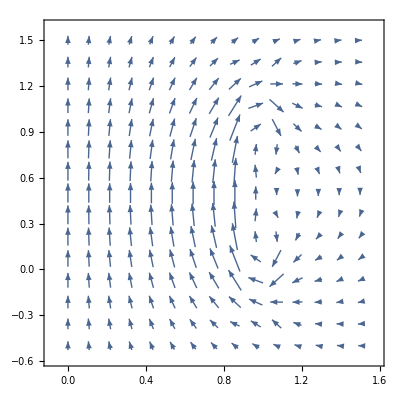

```mathematica
ListVectorPlot[v6]
```

What does the z-component of the B-field look like along the z-axis?

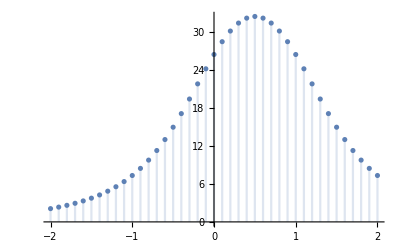

```mathematica
DiscretePlot[bloop[0,z][[3]]+bloop[0,z-0.2][[3]]+bloop[0,z-0.4][[3]]+bloop[0,z-0.6][[3]]+bloop[0,z-0.8][[3]]+bloop[0,z-1][[3]],{z,-2,2,.1}]
```

Let’s ONLY consider the B-field at the z-axis, and let’s try to design a solenoid that has UNIFORM Bz along the z-axis for at least some distance...

```mathematica
vn[dz_,N_]:=DiscretePlot[Sum[bloop[0,z-i*dz][[3]],{i,0,N}],{z,-0.5,N*dz+0.5,dz}]
```

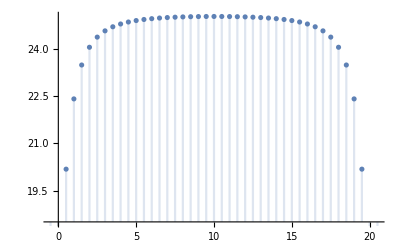

```mathematica
vn[0.5,40]
```

After playing around with your inputs, you will start to see that in order to get a uniform Bz, you need the length of the solenoid to be >> r!

## Our First CDF!

In our previous Computer Lab Lecture, we showed how we could develop plots that we could manipulate in real time.  The next logical step is to create a CDF, or Computable Document Format, file which can act as a stand-alone file (or an html file), which allows real time manipulation of the system under study.
To do this, we are going to open a new file, where we will again play around with the summation of cosines.  
Once you have created the file with the summation of Cosines, and if you have time, go ahead and create an additional CDF file that illuminates some aspect of today’s lecture.  This could be a CDF that plots Bz vs z for varying current, loops, and loop density, or a CDF that shows the vector field from a single loop, as a function of radius and current, to give just two examples. Of course, feel free to copy the code from this notebook as needed!